```mathematica
Get["C:\\Users\\diogo\\Desktop\\mathematica\\ValidacaoWellCat2.m"]
Get["C:\\Users\\diogo\\Dropbox\\Projeto PETRO\\Aquivos Mathematica\\diversos\\FORM.m"]
Get["C:\\Users\\diogo\\Dropbox\\Projeto PETRO\\Aquivos Mathematica\\diversos\\ModelIncludes.m"]
```

```mathematica
ComputeInitialPressure[Geometry_,Fluid_]:=Block[{PI,PE,ppgfttoPSI=0.0519481,L0,Lf,TOC,dl,RhoDisplace,RhoCement,RhoPreviusFase,lvec,PIplot,PEplot,diffini},
{L0,Lf,TOC,dl,lvec}=Geometry;
{RhoDisplace,RhoCement,RhoPreviusFase}=Fluid;
(*lvec=Table[dl,{dl,L0,Lf,dl}];*)
PI=Table[lvec[[i]]  RhoDisplace ppgfttoPSI,{i,1,Length[lvec]}];
PE=Table[If[lvec[[i]] <TOC,lvec[[i]]  RhoPreviusFase ppgfttoPSI,TOC ppgfttoPSI RhoPreviusFase+(lvec[[i]]-TOC)ppgfttoPSI RhoCement],{i,1,Length[lvec]}];
PIplot=Table[{PI[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
PEplot=Table[{PE[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
diffini=Table[{-PE[[i]]+PI[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
{PIplot,PEplot,diffini,PI,PE}
];
```

```mathematica
ComputeKickPressure[KickData_,Lvec_]:=Block[{diffini,PEplot,PIplot,PE,TOC,RhoWater,MaxMudDensityAnular,PI,Psurf,ppgfttoPSI=0.0519481,FracDepth,FracDensity,MaxMudDensity,KickIntensity},
{FracDepth,FracDensity,MaxMudDensity,KickIntensity,RhoWater,MaxMudDensityAnular,TOC}=KickData;
(*If[FracDensity FracDepth ppgfttoPSI> ]*)
Psurf=FracDepth ppgfttoPSI KickIntensity;
PI=Table[Psurf+ppgfttoPSI Lvec[[i]] MaxMudDensity,{i,1, Length[Lvec]}];
PE=Table[If[Lvec[[i]] <TOC,Lvec[[i]]  MaxMudDensityAnular ppgfttoPSI,TOC ppgfttoPSI MaxMudDensityAnular+(Lvec[[i]]-TOC)ppgfttoPSI RhoWater],{i,1,Length[Lvec]}];
PIplot=Table[{PI[[i]],-Lvec[[i]]},{i,1,Length[Lvec]}];
PEplot=Table[{PE[[i]],-Lvec[[i]]},{i,1,Length[Lvec]}];
diffini=Table[{-PE[[i]]+PI[[i]],-Lvec[[i]]},{i,1,Length[Lvec]}];
{PIplot,PEplot,diffini,PI,PE}
]
```

```mathematica
ComputeFullEvacuation[EvacData_,Lvec_]:=Block[{insidefluiddensity,percentevac,ppgfttoPSI=0.0519481,rhoar=0.0106437,PI,anulardensity,PE,PIplot,PEplot,diffini,depth,mult,EVD},
{anulardensity,insidefluiddensity,percentevac}=EvacData;
depth=Lvec[[Length[Lvec]]]-Lvec[[1]];
EVD=percentevac/100. depth;
PI=Table[If[Lvec[[i]]≤EVD, ppgfttoPSI Lvec[[i]] rhoar,ppgfttoPSI EVD rhoar+(Lvec[[i]]-EVD)ppgfttoPSI insidefluiddensity],{i,1 ,Length[Lvec]}];
PE=Table[Lvec[[i]]  anulardensity ppgfttoPSI,{i,1,Length[Lvec]}];
PIplot=Table[{PI[[i]],-Lvec[[i]]},{i,1,Length[Lvec]}];
PEplot=Table[{PE[[i]],-Lvec[[i]]},{i,1,Length[Lvec]}];
diffini=Table[{-PE[[i]]+PI[[i]],-Lvec[[i]]},{i,1,Length[Lvec]}];
{PIplot,PEplot,diffini,PI,PE}
]
```

```mathematica
ComputeTemperatureProfiles[TempData_]:=Block[{n,Tf,T0,dt,T,Lvec,Tplot,t,i,lvecold},
{T0,Tf,Lvec,lvecold}=TempData;
n=Length[lvecold]-1;
dt=(Tf-T0)/n;
T={};
t=T0;
For[i=1,i≤n+1,i++,
AppendTo[T,t];
t+=dt;
];
Print["Length[lvecold]= ",Length[lvecold]];
Print["Length[Lvec]",Length[Lvec]];

T=MakeCompatibleSizeVectors[Lvec,lvecold,T];
Print["Length[T] =",Length[T]];
Print["Length[lvecold]= ",Length[lvecold]];
Print["Length[Lvec]",Length[Lvec]];
(*T=Table[0,{n+1}];
T[[1]]=T0;
Table[T[[i]]=T[[i-1]]+dt,{i,2,n+1}];*)

(*Tplot=Table[{T[[i]],-Lvec[[i]]},{i,1,n+1}];*)
Tplot=Table[{T[[i]],-Lvec[[i]]},{i,1,Length[T]}];
{Tplot,T}
]
```

```mathematica
ComputeTemperatureProfiles[TempData_]:=Block[{n,Tf,T0,dt,T,Lvec,Tplot,t,i,lvecold,tt},
{T0,Tf,Lvec}=TempData;

sz=Length[Lvec];
y[h_]:=(Tf-T0)/(Lvec[[sz]]-Lvec[[1]])h;
dt=(Tf-T0)/sz;
T=Table[0,{sz},{2}];
tt=Table[0,{sz}];
t=T0;
For[i=1,i≤sz,i++,
T[[i,1]]=y[Lvec[[i]]];
T[[i,2]]=-Lvec[[i]];
tt[[i]]=T[[i,1]];
t+=dt;
];
{T,tt}
]
```

# -Graphics-

# -Graphics-

```mathematica
Lvec
```

Lvec

```mathematica
Clear[alfa,nu,young,weightperfeet,de,di,t,area,sigy,L0,Lf,TOC,diplacefluid,cementslurry,previousfasefluid,PIini,PEini,PIfim,PEfim,Tundisturbed,Tdisturbed,Lvec,PipeData,FiPlot,FfinalPlot,Fi,Ffinal,FracDepth,FracDensity,MaxMudDensity,KickIntensity,RhoWater,MaxMudDensityAnular,TOC,T0fim,Tfini,dl,Tf,T0,Fluid,Geometry,kickvec,InternalpressureInitialplot,ExternalpressureInitialplot,diffini,PIplot,PEplot,difffim,InitialProf,FinalProf]
(*Step Size*)
nn=30;

(*Casing Data*)
alfa=6.9 10^-6;
nu=0.30;
young=3 10^7;
weightperfeet=53.5;
de=9.625;
di=8.535;
t=(de-di)/2;
area=Pi/4(de^2-di^2);
sigy=80000;
PipeData={di,de,alfa,nu,young,weightperfeet,TOC};


(*Initial Conditions Data*)
diplacefluid=14.5;
cementslurry=15.8;
previousfasefluid=14.5;
L0=0.;
Lf=15000.;
TOC=9500.;
dl=(Lf-L0)/nn;
Lvecold=Table[dl,{dl,L0,Lf,dl}];
Lvec=refine[Lvecold,9499,9501,nn/2];
Fluid={diplacefluid,cementslurry,previousfasefluid};
Geometry={L0,Lf,TOC,dl,Lvec};

(*Kick Data*)
FracDepth=17500;
FracDensity=19.2;
MaxMudDensity=17.5;
KickIntensity=0.5;
RhoWater=8.33;
MaxMudDensityAnular=14.50;
kickvec={FracDepth,FracDensity,MaxMudDensity,KickIntensity,RhoWater,MaxMudDensityAnular,TOC};

(*Temperature Data*)
Tfini=331.1;
T0ini=40.;
Tffim=331.4;
T0fim=40.;

(*computing initial pressure*)
{InternalpressureInitialplot,ExternalpressureInitialplot,diffini,PIini,PEini}=ComputeInitialPressure[Geometry,Fluid];
(*computing kick pressure*)
{PIplot,PEplot,difffim,PIfim,PEfim}=ComputeKickPressure[kickvec,Lvec];
(*computing temperature profiles*)
{InitialProf,Tundisturbed}=ComputeTemperatureProfiles[{T0ini,Tfini,Lvec}];
{FinalProf,Tdisturbed}=ComputeTemperatureProfiles[{T0fim,Tffim,Lvec}];
(*computing Axial Forces*)
{FiPlot,FfinalPlot,Fi,Ffinal}=ComputeForces[PIini,PEini,PIfim,PEfim,Tundisturbed,Tdisturbed,Lvec,PipeData];

(*Plots*)
initialpressure=ListLinePlot[{InternalpressureInitialplot,ExternalpressureInitialplot,diffini},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Pressure (psi)","Initial Conditions"}},PlotLegends->{"P_i","P_e","ΔP"},LabelStyle->Directive[11],PlotMarkers->{"X","O","□", "◇","I"}]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\initialpressure.jpg",initialpressure,ImageResolution->300]

kickpressure=ListLinePlot[{PIplot,PEplot,difffim},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Pressure (psi)","Kick Loading"}},PlotLegends->{"P_i","P_e","ΔP"},LabelStyle->Directive[11],PlotMarkers->{"X","O","□", "◇","I"}]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\kickpressure.jpg",kickpressure,ImageResolution->300]

temperature=ListLinePlot[{InitialProf,FinalProf},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Temperature (F°)","Temperature Profiles"}},PlotLegends->{"T_i","T_f"}(*,PlotMarkers->{"X","O","□", "◇","I"}*),LabelStyle->Directive[11],PlotMarkers->{"X","O","□", "◇","I"}]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\temperature.jpg",temperature,ImageResolution->300]

axialload=ListLinePlot[{FiPlot,FfinalPlot},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Force (lbf)"," Axial Loading"}},PlotLegends->{"F_initial","F_final"}(*,PlotMarkers->{"X","O","□", "◇","I"}*),LabelStyle->Directive[11],PlotMarkers->{"X","O","□", "◇","I"}]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\axialload.jpg",axialload,ImageResolution->300]
```

primeiro livre

-Graphics-

C:\Users\diogo\Dropbox\figuraspaper\initialpressure.jpg

-Graphics-

C:\Users\diogo\Dropbox\figuraspaper\kickpressure.jpg

-Graphics-

C:\Users\diogo\Dropbox\figuraspaper\temperature.jpg

-Graphics-

C:\Users\diogo\Dropbox\figuraspaper\axialload.jpg

```mathematica
KSRandomVarsData={{"meKS","NORMAL",1.004, 0.047*1.004},{"APIyield","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Nax","NORMAL",1.0,0.001},{"Pext","NORMAL",1.0,0.001},{"Pint","NORMAL",1.0,0.001}};
KSRandomVarsDataA={{"meKS","NORMAL",1.004, 0.047*1.004},{"APIyield","NORMAL",1.0938,0.033*1.0938},{"Thickness","NORMAL",0.9876,0.002*0.9876},{"Nax","NORMAL",1.0,0.001},{"Pext","NORMAL",1.0,0.001},{"Pint","NORMAL",1.0,0.001}};
KSRandomVarsDataB={{"meKS","NORMAL",1.004, 0.047*1.004},{"APIyield","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",0.985,0.001*0.985},{"Nax","NORMAL",1.0,0.001},{"Pext","NORMAL",1.0,0.001},{"Pint","NORMAL",1.0,0.001}};

(*Vetor da Média*)
M=Transpose[KSRandomVarsData][[3]];
(*Vetor do Desvio Padrão*)
SDev=Transpose[KSRandomVarsData][[4]];
(*Vetor das Distribuições*)
distr=Transpose[KSRandomVarsData][[2]];
nvars=Length[M];
RX=IdentityMatrix[nvars];
(*Informações sobre as variáveis aleatórias*)
RVVec=Table[ComputeRandomVarData[distr[[i]],M[[i]],SDev[[i]]],{i,1,nvars}];


vars=Table[{de,t,sigy,Ffinal[[i]]/area,PIfim[[i]],PEfim[[i]]},{i,1,Length[Ffinal]}];

(*Cálculo de GX e GRADGX de Klever-Stewart*)
ComputeNumericalGradKS[vars[[3]],M]
(*Verificação do cálculo da derivada*)
Table[checkconv[vars[[i]],M,ComputeNumericalGradKS],{i,1,1}]

(*FORM Para Klever-Stewart*)
KSsol=Table[HRLF[RVVec,RX,ComputeNumericalGradKS,vars[[i]]],{i,1,Length[vars]}];
plotbetaKS=Table[{KSsol[[i]][[1]],-Lvec[[i]]},{i,1,Length[Lvec]}];
alfaKS=Table[KSsol[[i]][[4]],{i,1,Length[Lvec]}];

(*FORM Para Barlow*)
varsb=Table[{de,sigy,t,PIfim[[i]],PEfim[[i]]},{i,1,Length[PIfim]}];
BAsol=Table[HRLF[RVVec,RX,ComputeBurstBarlow,varsb[[i]]],{i,1,Length[vars]}];
plotbetaBA=Table[{BAsol[[i]][[1]],-Lvec[[i]]},{i,1,Length[Lvec]}];
alfaBA=Table[BAsol[[i]][[4]],{i,1,Length[Lvec]}];


(*Fatores de Segurança Para Barlow e Klever-Stewart*)
SFBarlow=Table[{ComputeBurstBarlow[{de,sigy,t,PIfim[[i]],PEfim[[i]]}]/(PIfim[[i]]-PEfim[[i]]),-Lvec[[i]]},{i,2,Length[Lvec]}];
SFKS=Table[{ComputeDuctileRupture[de,t,sigy ,Ffinal[[i]]/area,PEfim[[i]],PIfim[[i]]]/(PIfim[[i]]-PEfim[[i]]),-Lvec[[i]]},{i,1,Length[Lvec]}];


sfbeta=ListLinePlot[{SFBarlow,SFKS,plotbetaKS,plotbetaBA},Frame->True,FrameLabel->{{" Depth(ft)",""},{"Safety Factor and Reliability Index","Safety Factor and Reliability Index"}},PlotLegends->{"γ_B","γ_KS","β_RKS","β_RB"},(*PlotMarkers->{"X","O","□", "◇","I"}*)LabelStyle->Directive[11],PlotMarkers->{"X","O","□", "◇","I"}]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\sfbeta.jpg",sfbeta,ImageResolution->300]
```

{10172.7,{10740.1,9331.25,10476.,188.776,1513.23,-1363.64}}

tan = {9998.51,9378.62,10481.8,155.503,0.,-454.546}

incval = {0.000960196,0.00365424,0.00265619,0.00338308,0.00196277,0.00394591}

estimateresidual = 70.4464

2.00034

2.00032

2.00036

2.00042

2.00048

2.00055

2.00062

2.0007

{{0.00165026,0.00660257,0.0148577,0.0264164,0.0412795,0.0594478,0.0809219,0.105703,0.133791,0}}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-Graphics-

C:\Users\diogo\Dropbox\figuraspaper\sfbeta.jpg

```mathematica
Ffinal
```

{647037.,620287.,593537.,566787.,540037.,513287.,486537.,459787.,433037.,406287.,379537.,352787.,326037.,299287.,272537.,245787.,219037.,192287.,165537.,138841.,138834.,138827.,138819.,138812.,138805.,138798.,138791.,138787.,157383.,157379.,157375.,157371.,157366.,157362.,157358.,157354.,141748.,126111.,110474.,94837.6,79200.7,63563.8,47926.9,32290.,16653.1,1016.22,-14620.7}

```mathematica
Clear[alfa,nu,young,weightperfeet,de,di,t,area,sigy,L0,Lf,TOC,diplacefluid,cementslurry,previousfasefluid,PIini,PEini,PIfim,PEfim,Tundisturbed,Tdisturbed,Lvec,PipeData,FiPlot,FfinalPlot,Fi,Ffinal,FracDepth,FracDensity,MaxMudDensity,KickIntensity,RhoWater,MaxMudDensityAnular,TOC,T0fim,Tfini,dl,Tf,T0,Fluid,Geometry,kickvec,InternalpressureInitialplot,ExternalpressureInitialplot,diffini,PIplot,PEplot,difffim,InitialProf,FinalProf]
(*Step Size*)
nn=30;

(*Casing Data*)
alfa=6.9 10^-6;
nu=0.30;
young=3 10^7;
weightperfeet=38;
de=7;
di=5.920;
t=(de-di)/2;
area=Pi/4(de^2-di^2);
sigy=125000;
PipeData={di,de,alfa,nu,young,weightperfeet,TOC};


(*Initial Conditions Data*)
diplacefluid=17.5;
cementslurry=15.8;
previousfasefluid=17.5;

L0=0.;
Lf=14800.;
TOC=14800;
dl=(Lf-L0)/nn;
Lvecold=Table[dl,{dl,L0,Lf,dl}];
Lvec=Lvecold;
(*Lvec=refine[Lvecold,0,1,nn/2];*)


Fluid={diplacefluid,cementslurry,previousfasefluid};
Geometry={L0,Lf,TOC,dl,Lvec};

(*Evacuation Data Data*)
AnularDensity=17.5;
InsideFluidDensity=8.33;
percentevac=100;
EvacuatedData={AnularDensity,InsideFluidDensity,percentevac};

(*Temperature Data*)
Tfini=327.2;
T0ini=40.;
Tffim=327.2;
T0fim=40.;


(*computing initial pressure*)
{InternalpressureInitialplot,ExternalpressureInitialplot,diffini,PIini,PEini}=ComputeInitialPressure[Geometry,Fluid];
(*computing kick pressure*)
{PIplot,PEplot,difffim,PIfim,PEfim}=ComputeFullEvacuation[EvacuatedData,Lvec];
(*computing temperature profiles*)
{InitialProf,Tundisturbed}=ComputeTemperatureProfiles[{T0ini,Tfini,Lvec}];
{FinalProf,Tdisturbed}=ComputeTemperatureProfiles[{T0fim,Tffim,Lvec}];
(*computing Axial Forces*)
{FiPlot,FfinalPlot,Fi,Ffinal}=ComputeForces[PIini,PEini,PIfim,PEfim,Tundisturbed,Tdisturbed,Lvec,PipeData];

(*Plots*)
initialpressure=ListLinePlot[{InternalpressureInitialplot,ExternalpressureInitialplot,diffini},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Pressure (psi)","Initial Conditions"}},PlotLegends->{"P_i","P_e","ΔP"},LabelStyle->Directive[11],PlotMarkers->{"X","O","□", "◇","I"}]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\initialpressurekt.jpg",initialpressure,ImageResolution->300]

fullvacpressure=ListLinePlot[{PIplot,PEplot,difffim},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Pressure (psi)","Kick Loading"}},PlotLegends->{"P_i","P_e","ΔP"},LabelStyle->Directive[11],PlotMarkers->{"X","O","□", "◇","I"}]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\fullvacpressure.jpg",fullvacpressure,ImageResolution->300]

temperature=ListLinePlot[{InitialProf,FinalProf},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Temperature (F°)","Temperature Profiles"}},PlotLegends->{"T_i","T_f"},PlotMarkers->{"X","O","□", "◇","I"},LabelStyle->Directive[11]]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\temperaturekt.jpg",temperature,ImageResolution->300]

axialload=ListLinePlot[{FiPlot,FfinalPlot},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Force (lbf)"," Axial Loading"}},PlotLegends->{"F_initial","F_final"},PlotMarkers->{"X","O","□", "◇","I"},LabelStyle->Directive[11]]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\axialloadkt.jpg",axialload,ImageResolution->300]
```

primeiro livre

-Graphics-

C:\Users\diogo\Dropbox\figuraspaper\initialpressurekt.jpg

-Graphics-

C:\Users\diogo\Dropbox\figuraspaper\fullvacpressure.jpg

-Graphics-

C:\Users\diogo\Dropbox\figuraspaper\temperaturekt.jpg

-Graphics-

C:\Users\diogo\Dropbox\figuraspaper\axialloadkt.jpg

```mathematica
Ffinal
```

{307616.,288869.,270123.,251376.,232629.,213883.,195136.,176389.,157643.,138896.,120149.,101403.,82655.9,63909.3,45162.6,26415.9,7669.26,-11077.4,-29824.1,-48570.7,-67317.4,-86064.1,-104811.,-123557.,-142304.,-161051.,-179797.,-198544.,-217291.,-236037.,-254784.}

```mathematica
Lvec
```

{0.,493.333,986.667,1480.,1973.33,2466.67,2960.,3453.33,3946.67,4440.,4933.33,5426.67,5920.,6413.33,6906.67,7400.,7893.33,8386.67,8880.,9373.33,9866.67,10360.,10853.3,11346.7,11840.,12333.3,12826.7,13320.,13813.3,14306.7,14800.}

```mathematica
(*Dados sobre variáveis aleatórias retirados da ISO 10400*)
KTRandomVarsData={{"KTme","NORMAL",0.9991,0.067*0.9991},{"YieldStress","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Ovality","NORMAL",0.217,0.541*0.217},{"Excent","NORMAL",3.924,0.661*3.924},{"Resid. Stress","NORMAL",-0.237,0.332*0.237},{"Nax","NORMAL",1.,0.01},{"Pint","NORMAL",1.,0.01},{"Pext","NORMAL",1.,0.01}}
ov=0.217;
ex=3.924;
rs=-0.237;
(*Vetor da Média*)
M=Transpose[KTRandomVarsData][[3]];
(*Vetor do Desvio Padrão*)
SDev=Transpose[KTRandomVarsData][[4]];
(*Vetor das Distribuições*)
distr=Transpose[KTRandomVarsData][[2]];
nvars=Length[M];
RX=IdentityMatrix[nvars];
(*Informações sobre as variáveis aleatórias*)
RVVec=Table[ComputeRandomVarData[distr[[i]],M[[i]],SDev[[i]]],{i,1,nvars}]
vars=Table[{Ffinal[[i]]/area,sigy,PIfim[[i]],PEfim[[i]],de,t,3 10^7,0.3},{i,1,Length[Ffinal]}];

(*Cálculo de GX e GRADGX de API*)
ComputeNumericalGradAPI[vars[[3]],M]
(*Verificação do cálculo da derivada*)
Table[checkconv[vars[[i]],M,ComputeNumericalGradAPI],{i,1,1}]

(*Cálculo de GX e GRADGX de API*)
ComputeNumericalGradKT[vars[[3]],M]
(*Verificação do cálculo da derivada*)
Table[checkconv[vars[[i]],M,ComputeNumericalGradKT],{i,1,1}]
```

{{KTme,NORMAL,0.9991,0.0669397},{YieldStress,NORMAL,1.1,0.04642},{Thickness,NORMAL,1.0069,0.0260787},{Ovality,NORMAL,0.217,0.117397},{Excent,NORMAL,3.924,2.59376},{Resid. Stress,NORMAL,-0.237,0.078684},{Nax,NORMAL,1.,0.01},{Pint,NORMAL,1.,0.01},{Pext,NORMAL,1.,0.01}}

{{0.9991,0.0669397,0.9991,0.0669397,1},{1.1,0.04642,1.1,0.04642,1},{1.0069,0.0260787,1.0069,0.0260787,1},{0.217,0.117397,0.217,0.117397,1},{3.924,2.59376,3.924,2.59376,1},{-0.237,0.078684,-0.237,0.078684,1},{1.,0.01,1.,0.01,1},{1.,0.01,1.,0.01,1},{1.,0.01,1.,0.01,1}}

{15902.6,{0.,13576.6,30802.8,0.,0.,0.,-1682.31,0.545548,-896.971}}

tan = {0.,13733.1,30171.2,0.,0.,0.,-1989.86,0.,0.}

incval = {0.00122206,0.00379296,0.00401742,0.000817788,0.0022786,-0.000475589,0.00458767,0.0032497,0.00341103}

estimateresidual = 164.171

1.97736

1.98703

1.9909

1.99302

1.99437

1.99532

1.99602

1.99656

{{0.00438768,0.0172774,0.0386703,0.0685674,0.10697,0.153878,0.209294,0.273219,0.345653,0}}

{13523.,{14432.4,12459.3,20367.5,-1214.76,-37.3043,4209.01,-2001.73,1.0463,-896.971}}

tan = {14147.7,12693.7,19709.1,-1162.61,-35.7028,4028.3,-2380.38,0.,0.}

incval = {0.00149547,0.00355563,0.000768448,0.000992913,0.00845689,-0.000450406,0.00493535,0.00151103,0.00316903}

estimateresidual = 66.4185

1.83252

1.89674

1.92495

1.94099

1.9514

1.9587

1.96412

1.9683

{{0.00101906,0.00362947,0.00783145,0.0136252,0.0210109,0.0299887,0.0405589,0.0527217,0.0664772,0}}

```mathematica
(*FORM Para Klever-Tamano*)
KTsol=Table[HRLF[RVVec,RX,ComputeNumericalGradKT,vars[[i]]],{i,1,Length[vars]}];
plotbetaKT=Table[{KTsol[[i]][[1]],-Lvec[[i]]},{i,1,Length[Lvec]}];
alfaKT=Table[KTsol[[i]][[4]],{i,1,Length[Lvec]}];

(*FORM Para API*)
APIsol=Table[HRLF[RVVec,RX,ComputeNumericalGradAPI,vars[[i]]],{i,1,Length[vars]}];
plotbetaAPI=Table[{APIsol[[i]][[1]],-Lvec[[i]]},{i,1,Length[Lvec]}];
alfaAPI=Table[APIsol[[i]][[4]],{i,1,Length[Lvec]}];

(*Fatores de Segurança Para Klever-Tamano*)
SFKT=Table[{ComputeColapseStrengthKT[Ffinal[[i]]/area,sigy,PIfim[[i]],de,t,3 10^7,0.3,ov,ex,rs]/(PEfim[[i]]-PIfim[[i]]),-Lvec[[i]]},{i,1,Length[Lvec]}];

SFAPI=Table[{(ComputePipeStrength[Ffinal[[i]]/area,sigy,de,t,young,nu][[2]])/(PEfim[[i]]-PIfim[[i]]),-Lvec[[i]]},{i,1,Length[Lvec]}];

sfbeta=ListLinePlot[{SFKT,SFAPI,plotbetaKT,plotbetaAPI},Frame->True,FrameLabel->{{" Depth(ft)",""},{"Safety Factor and Reliability Index","Safety Factor and Reliability Index"}},PlotLegends->{"γ_KT","γ_API","β_RKT","β_RAPI"},PlotMarkers->{"X","O","□", "◇","I"},LabelStyle->Directive[11],PlotRange->{{0,17},{-Lf,L0}}]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\sfbetakt.jpg",sfbeta,ImageResolution->300]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with 81.0117+39.3555 ⅈ attempted.

LessEqual::nord: Invalid comparison with 41.4578+7.98166 ⅈ attempted.

LessEqual::nord: Invalid comparison with 81.0117+39.3555 ⅈ attempted.

LessEqual::nord: Invalid comparison with 41.4578+7.98166 ⅈ attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with 81.0117+39.3555 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with 80.9929+39.3696 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. (0.-ColapseStrength) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

-Graphics-

C:\Users\diogo\Dropbox\figuraspaper\sfbetakt.jpg

# Arquivo exemplomeu.wcd

# Revestimento Intermediário 13 5/8 Carregamento: Kick

primeiro livre

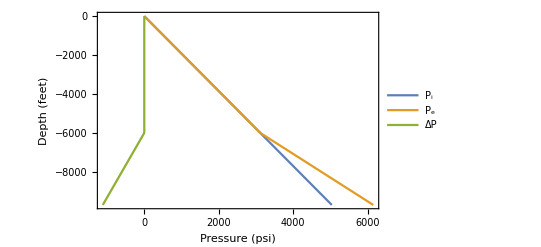

C:\Users\diogo\Dropbox\figuraspaper\initialpressurekt1358.jpg

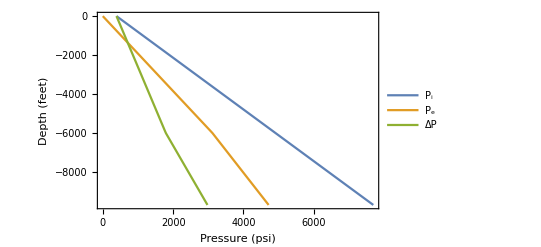

C:\Users\diogo\Dropbox\figuraspaper\fullvacpressure1358.jpg

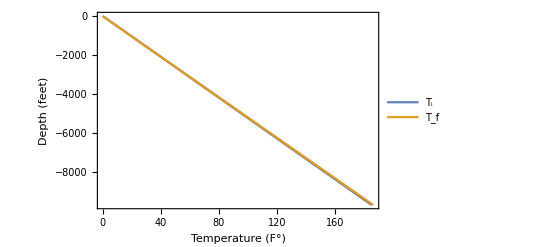

C:\Users\diogo\Dropbox\figuraspaper\temperaturekt1358.jpg

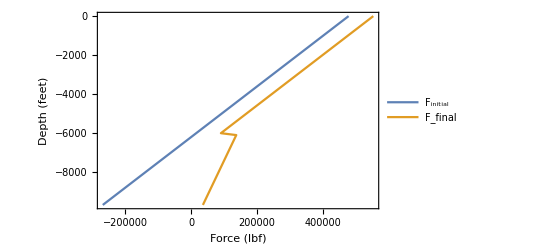

C:\Users\diogo\Dropbox\figuraspaper\axialloadkt1358.jpg

{6755.86,{7162.17,6525.61,7320.88,200.777,202.794,-535.741}}

tan = {7066.06,6529.86,7325.14,202.343,0.,-389.611}

incval = {0.00322682,0.0013554,0.00253982,0.0025737,0.00454814,0.000808682}

estimateresidual = 50.4618

2.00446

2.00266

2.00201

2.00169

2.00152

2.00142

2.00138

2.00136

{{0.00115915,0.00465094,0.0104759,0.0186346,0.0291276,0.0419553,0.0571184,0.0746173,0.0944527,0}}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

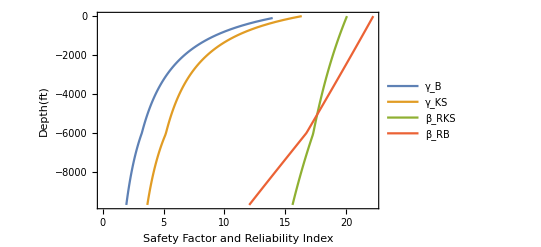

C:\Users\diogo\Dropbox\figuraspaper\sfbeta1358.jpg

```mathematica
Clear[alfa,nu,young,weightperfeet,de,di,t,area,sigy,L0,Lf,TOC,diplacefluid,cementslurry,previousfasefluid,PIini,PEini,PIfim,PEfim,Tundisturbed,Tdisturbed,Lvec,PipeData,FiPlot,FfinalPlot,Fi,Ffinal,FracDepth,FracDensity,MaxMudDensity,KickIntensity,RhoWater,MaxMudDensityAnular,TOC,T0fim,Tfini,dl,Tf,T0,Fluid,Geometry,kickvec,InternalpressureInitialplot,ExternalpressureInitialplot,diffini,PIplot,PEplot,difffim,InitialProf,FinalProf]
axwellcat={551987,548915,503023,457131,411239,398002,397987,365347,319455,274790,273563,227671,181779,135887,89994,138924,138910,131403,123882,118312,116363,108845,101324,97703,93805,86287,78768,77097,71251,63735,60951,58167,56496,55382,52598,49813,47028,44243,41457,38671,35885};
lwellcat={0,40,636,1232,1828,2000,2000,2424,3020,3600,3616,4212,4808,5404,6000,6000,6001,6270,6540,6740,6810,7080,7350,7480,7620,7890,8160,8220,8430,8700,8800,8900,8960,9000,9100,9200,9300,9400,9500,9600,9700};

plotaxwellcat=Table[{axwellcat[[i]],-lwellcat[[i]]},{i,1,Length[lwellcat]}];

(*Step Size*)
nn=100;

(*Casing Data*)
alfa=6.9 10^-6;
nu=0.30;
young=3 10^7;
weightperfeet=77;
de=13.375;
di=12.275;
t=(de-di)/2;
area=Pi/4(de^2-di^2);
sigy=80000;
PipeData={di,de,alfa,nu,young,weightperfeet,TOC};



(*Initial Conditions Data*)
diplacefluid=10;
cementslurry=15.8;
previousfasefluid=10;

L0=0.;
Lf=9700.;
TOC=6000;
dl=(Lf-L0)/nn;
Lvecold=Table[dl,{dl,L0,Lf,dl}];
Lvec=Lvecold;
(*Lvec=refine[Lvecold,0,1,nn/2];*)


Fluid={diplacefluid,cementslurry,previousfasefluid};
Geometry={L0,Lf,TOC,dl,Lvec};

(*Kick Data*)
FracDepth=15000;
FracDensity=15.81;
MaxMudDensity=14.5;
KickIntensity=0.5;
RhoWater=8.33;
MaxMudDensityAnular=10;
kickvec={FracDepth,FracDensity,MaxMudDensity,KickIntensity,RhoWater,MaxMudDensityAnular,TOC};

(*Temperature Data*)
Tfini=225.3;
T0ini=40.;
Tffim=226.5;
T0fim=40.;


(*computing initial pressure*)
{InternalpressureInitialplot,ExternalpressureInitialplot,diffini,PIini,PEini}=ComputeInitialPressure[Geometry,Fluid];
(*computing kick pressure*)
{PIplot,PEplot,difffim,PIfim,PEfim}=ComputeKickPressure[kickvec,Lvec];
(*computing temperature profiles*)
{InitialProf,Tundisturbed}=ComputeTemperatureProfiles[{T0ini,Tfini,Lvec}];
{FinalProf,Tdisturbed}=ComputeTemperatureProfiles[{T0fim,Tffim,Lvec}];
(*computing Axial Forces*)
{FiPlot,FfinalPlot,Fi,Ffinal}=ComputeForces[PIini,PEini,PIfim,PEfim,Tundisturbed,Tdisturbed,Lvec,PipeData];

(*Plots*)
initialpressure=ListLinePlot[{InternalpressureInitialplot,ExternalpressureInitialplot,diffini},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Pressure (psi)","Initial Conditions"}},PlotLegends->{"P_i","P_e","ΔP"}(*,PlotMarkers->{"X","O","□", "◇","I"}*)]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\initialpressurekt1358.jpg",initialpressure,ImageResolution->100]

fullvacpressure=ListLinePlot[{PIplot,PEplot,difffim},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Pressure (psi)","Kick Loading"}},PlotLegends->{"P_i","P_e","ΔP"}(*,PlotMarkers->{"X","O","□", "◇","I"}*)]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\fullvacpressure1358.jpg",fullvacpressure,ImageResolution->100]

temperature=ListLinePlot[{InitialProf,FinalProf},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Temperature (F°)","Temperature Profiles"}},PlotLegends->{"T_i","T_f"}(*,PlotMarkers->{"X","O","□", "◇","I"}*)]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\temperaturekt1358.jpg",temperature,ImageResolution->100]

axialload=ListLinePlot[{FiPlot,FfinalPlot},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Force (lbf)"," Axial Loading"}},PlotLegends->{"F_initial","F_final"}(*,PlotMarkers->{"X","O","□", "◇","I"}*),LabelStyle->Directive[11]]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\axialloadkt1358.jpg",axialload,ImageResolution->100] 
KSRandomVarsData={{"meKS","NORMAL",1.004, 0.047*1.004},{"APIyield","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Nax","NORMAL",1.0,0.001},{"Pext","NORMAL",1.0,0.001},{"Pint","NORMAL",1.0,0.001}};
KSRandomVarsDataA={{"meKS","NORMAL",1.004, 0.047*1.004},{"APIyield","NORMAL",1.0938,0.033*1.0938},{"Thickness","NORMAL",0.9876,0.002*0.9876},{"Nax","NORMAL",1.0,0.001},{"Pext","NORMAL",1.0,0.001},{"Pint","NORMAL",1.0,0.001}};
KSRandomVarsDataB={{"meKS","NORMAL",1.004, 0.047*1.004},{"APIyield","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",0.985,0.001*0.985},{"Nax","NORMAL",1.0,0.001},{"Pext","NORMAL",1.0,0.001},{"Pint","NORMAL",1.0,0.001}};

(*Vetor da Média*)
M=Transpose[KSRandomVarsData][[3]];
(*Vetor do Desvio Padrão*)
SDev=Transpose[KSRandomVarsData][[4]];
(*Vetor das Distribuições*)
distr=Transpose[KSRandomVarsData][[2]];
nvars=Length[M];
RX=IdentityMatrix[nvars];
(*Informações sobre as variáveis aleatórias*)
RVVec=Table[ComputeRandomVarData[distr[[i]],M[[i]],SDev[[i]]],{i,1,nvars}];


vars=Table[{de,t,sigy,Ffinal[[i]]/area,PIfim[[i]],PEfim[[i]]},{i,1,Length[Ffinal]}];

(*Cálculo de GX e GRADGX de Klever-Stewart*)
ComputeNumericalGradKS[vars[[3]],M]
(*Verificação do cálculo da derivada*)
Table[checkconv[vars[[i]],M,ComputeNumericalGradKS],{i,1,1}]

(*FORM Para Klever-Stewart*)
KSsol=Table[HRLF[RVVec,RX,ComputeNumericalGradKS,vars[[i]]],{i,1,Length[vars]}];
plotbetaKS=Table[{KSsol[[i]][[1]],-Lvec[[i]]},{i,1,Length[Lvec]}];
alfaKS=Table[KSsol[[i]][[4]],{i,1,Length[Lvec]}];

(*FORM Para Barlow*)
varsb=Table[{de,sigy,t,PIfim[[i]],PEfim[[i]]},{i,1,Length[PIfim]}];
BAsol=Table[HRLF[RVVec,RX,ComputeBurstBarlow,varsb[[i]]],{i,1,Length[vars]}];
plotbetaBA=Table[{BAsol[[i]][[1]],-Lvec[[i]]},{i,1,Length[Lvec]}];
alfaBA=Table[BAsol[[i]][[4]],{i,1,Length[Lvec]}];


(*Fatores de Segurança Para Barlow e Klever-Stewart*)
SFBarlow=Table[{ComputeBurstBarlow[{de,sigy,t,PIfim[[i]],PEfim[[i]]}]/(PIfim[[i]]-PEfim[[i]]),-Lvec[[i]]},{i,2,Length[Lvec]}];
SFKS=Table[{ComputeDuctileRupture[de,t,sigy ,Ffinal[[i]]/area,PEfim[[i]],PIfim[[i]]]/(PIfim[[i]]-PEfim[[i]]),-Lvec[[i]]},{i,1,Length[Lvec]}];


sfbeta=ListLinePlot[{SFBarlow,SFKS,plotbetaKS,plotbetaBA},Frame->True,FrameLabel->{{" Depth(ft)",""},{"Safety Factor and Reliability Index","Safety Factor and Reliability Index"}},PlotLegends->{"γ_B","γ_KS","β_RKS","β_RB"}(*PlotMarkers->{"X","O","□", "◇","I"}*)]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\sfbeta1358.jpg",sfbeta,ImageResolution->100]
```

# Protective Casing 9 5/8 Carregamento: Kick

primeiro livre

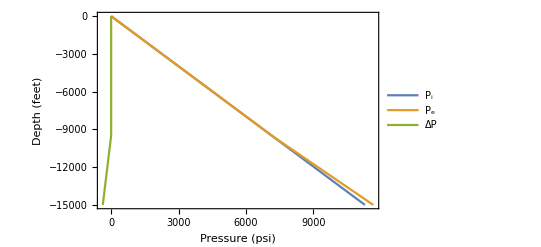

C:\Users\diogo\Dropbox\figuraspaper\initialpressurekt958.jpg

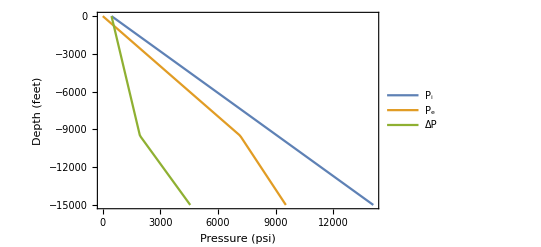

C:\Users\diogo\Dropbox\figuraspaper\fullvacpressure958.jpg

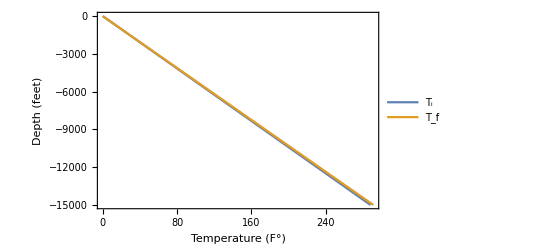

C:\Users\diogo\Dropbox\figuraspaper\temperaturekt958.jpg

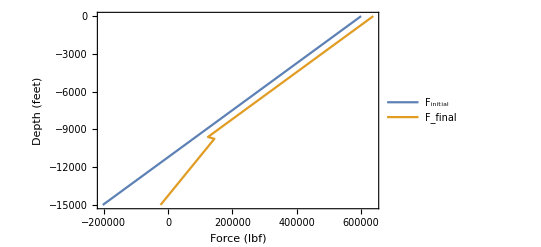

C:\Users\diogo\Dropbox\figuraspaper\axialloadkt958.jpg

{9758.36,{10218.8,9353.28,10479.2,174.895,453.841,-727.273}}

tan = {9996.18,9367.64,10480.8,164.492,0.,-454.546}

incval = {0.00384689,0.0000555529,0.00328766,0.00481692,0.000878873,0.00495544}

estimateresidual = 71.9718

1.99946

1.99964

1.99969

1.99971

1.99971

1.9997

1.99968

1.99966

{{0.00137184,0.0054853,0.0123401,0.0219361,0.0342729,0.0493503,0.0671681,0.0877261,0.111024,0}}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

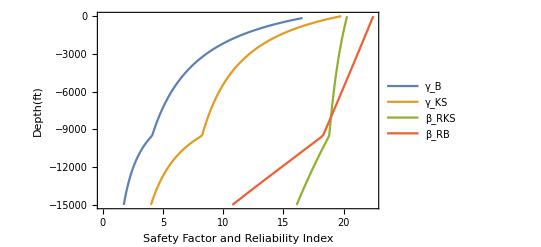

C:\Users\diogo\Dropbox\figuraspaper\sfbeta958.jpg

```mathematica
Clear[alfa,nu,young,weightperfeet,de,di,t,area,sigy,L0,Lf,TOC,diplacefluid,cementslurry,previousfasefluid,PIini,PEini,PIfim,PEfim,Tundisturbed,Tdisturbed,Lvec,PipeData,FiPlot,FfinalPlot,Fi,Ffinal,FracDepth,FracDensity,MaxMudDensity,KickIntensity,RhoWater,MaxMudDensityAnular,TOC,T0fim,Tfini,dl,Tf,T0,Fluid,Geometry,kickvec,InternalpressureInitialplot,ExternalpressureInitialplot,diffini,PIplot,PEplot,difffim,InitialProf,FinalProf]

axwellcat={623694,621560,570949,522045,520338,469727,420396,419116,368505,318747,317894,267283,217099,216672,166061,115450,150822,150806,144479,144484,136567,122319,115988,108073,93824,81160,79578,65330,51083,46335,36837,22591,11511,8345,5179,2012,-1154,-4321,-7488,-10654,-13821,-16988,-20154,-23321};
lwellcat={0,40,986,1900,1932,2878,3800,3824,4770,5700,5716,6662,7600,7608,8554,9500,9500,9501,9700,9700,9950,10400,10600,10850,11300,11700,11750,12200,12650,12800,13100,13550,13900,14000,14100,14200,14300,14400,14500,14600,14700,14800,14900,15000};

plotaxwellcat=Table[{axwellcat[[i]],-lwellcat[[i]]},{i,1,Length[lwellcat]}];

(*Step Size*)
nn=100;

(*Casing Data*)
alfa=6.9 10^-6;
nu=0.30;
young=3 10^7;
weightperfeet=53.5;
de=9.625;
di=8.535;
t=(de-di)/2;
area=Pi/4(de^2-di^2);
sigy=80000;
PipeData={di,de,alfa,nu,young,weightperfeet,TOC};



(*Initial Conditions Data*)
diplacefluid=14.5;
cementslurry=15.8;
previousfasefluid=14.5;

L0=0.;
Lf=15000;
TOC=9500;
dl=(Lf-L0)/nn;
Lvecold=Table[dl,{dl,L0,Lf,dl}];
Lvec=Lvecold;
(*Lvec=refine[Lvecold,0,1,nn/2];*)


Fluid={diplacefluid,cementslurry,previousfasefluid};
Geometry={L0,Lf,TOC,dl,Lvec};

(*Kick Data*)
FracDepth=17500;
FracDensity=19.21;
MaxMudDensity=17.5;
KickIntensity=0.5;
RhoWater=8.33;
MaxMudDensityAnular=14.5;
kickvec={FracDepth,FracDensity,MaxMudDensity,KickIntensity,RhoWater,MaxMudDensityAnular,TOC};

(*Temperature Data*)
Tfini=328.4;
T0ini=40.;
Tffim=331.4;
T0fim=40.;


(*computing initial pressure*)
{InternalpressureInitialplot,ExternalpressureInitialplot,diffini,PIini,PEini}=ComputeInitialPressure[Geometry,Fluid];
(*computing kick pressure*)
{PIplot,PEplot,difffim,PIfim,PEfim}=ComputeKickPressure[kickvec,Lvec];
(*computing temperature profiles*)
{InitialProf,Tundisturbed}=ComputeTemperatureProfiles[{T0ini,Tfini,Lvec}];
{FinalProf,Tdisturbed}=ComputeTemperatureProfiles[{T0fim,Tffim,Lvec}];
(*computing Axial Forces*)
{FiPlot,FfinalPlot,Fi,Ffinal}=ComputeForces[PIini,PEini,PIfim,PEfim,Tundisturbed,Tdisturbed,Lvec,PipeData];

(*Plots*)
initialpressure=ListLinePlot[{InternalpressureInitialplot,ExternalpressureInitialplot,diffini},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Pressure (psi)","Initial Conditions"}},PlotLegends->{"P_i","P_e","ΔP"}(*,PlotMarkers->{"X","O","□", "◇","I"}*)]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\initialpressurekt958.jpg",initialpressure,ImageResolution->100]

fullvacpressure=ListLinePlot[{PIplot,PEplot,difffim},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Pressure (psi)","Kick Loading"}},PlotLegends->{"P_i","P_e","ΔP"}(*,PlotMarkers->{"X","O","□", "◇","I"}*)]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\fullvacpressure958.jpg",fullvacpressure,ImageResolution->100]

temperature=ListLinePlot[{InitialProf,FinalProf},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Temperature (F°)","Temperature Profiles"}},PlotLegends->{"T_i","T_f"}(*,PlotMarkers->{"X","O","□", "◇","I"}*)]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\temperaturekt958.jpg",temperature,ImageResolution->100]

axialload=ListLinePlot[{FiPlot,FfinalPlot},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Force (lbf)"," Axial Loading"}},PlotLegends->{"F_initial","F_final"}(*,PlotMarkers->{"X","O","□", "◇","I"}*),LabelStyle->Directive[11]]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\axialloadkt958.jpg",axialload,ImageResolution->100] 
KSRandomVarsData={{"meKS","NORMAL",1.004, 0.047*1.004},{"APIyield","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Nax","NORMAL",1.0,0.001},{"Pext","NORMAL",1.0,0.001},{"Pint","NORMAL",1.0,0.001}};
KSRandomVarsDataA={{"meKS","NORMAL",1.004, 0.047*1.004},{"APIyield","NORMAL",1.0938,0.033*1.0938},{"Thickness","NORMAL",0.9876,0.002*0.9876},{"Nax","NORMAL",1.0,0.001},{"Pext","NORMAL",1.0,0.001},{"Pint","NORMAL",1.0,0.001}};
KSRandomVarsDataB={{"meKS","NORMAL",1.004, 0.047*1.004},{"APIyield","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",0.985,0.001*0.985},{"Nax","NORMAL",1.0,0.001},{"Pext","NORMAL",1.0,0.001},{"Pint","NORMAL",1.0,0.001}};

(*Vetor da Média*)
M=Transpose[KSRandomVarsData][[3]];
(*Vetor do Desvio Padrão*)
SDev=Transpose[KSRandomVarsData][[4]];
(*Vetor das Distribuições*)
distr=Transpose[KSRandomVarsData][[2]];
nvars=Length[M];
RX=IdentityMatrix[nvars];
(*Informações sobre as variáveis aleatórias*)
RVVec=Table[ComputeRandomVarData[distr[[i]],M[[i]],SDev[[i]]],{i,1,nvars}];


vars=Table[{de,t,sigy,Ffinal[[i]]/area,PIfim[[i]],PEfim[[i]]},{i,1,Length[Ffinal]}];

(*Cálculo de GX e GRADGX de Klever-Stewart*)
ComputeNumericalGradKS[vars[[3]],M]
(*Verificação do cálculo da derivada*)
Table[checkconv[vars[[i]],M,ComputeNumericalGradKS],{i,1,1}]

(*FORM Para Klever-Stewart*)
KSsol=Table[HRLF[RVVec,RX,ComputeNumericalGradKS,vars[[i]]],{i,1,Length[vars]}];
plotbetaKS=Table[{KSsol[[i]][[1]],-Lvec[[i]]},{i,1,Length[Lvec]}];
alfaKS=Table[KSsol[[i]][[4]],{i,1,Length[Lvec]}];

(*FORM Para Barlow*)
varsb=Table[{de,sigy,t,PIfim[[i]],PEfim[[i]]},{i,1,Length[PIfim]}];
BAsol=Table[HRLF[RVVec,RX,ComputeBurstBarlow,varsb[[i]]],{i,1,Length[vars]}];
plotbetaBA=Table[{BAsol[[i]][[1]],-Lvec[[i]]},{i,1,Length[Lvec]}];
alfaBA=Table[BAsol[[i]][[4]],{i,1,Length[Lvec]}];


(*Fatores de Segurança Para Barlow e Klever-Stewart*)
SFBarlow=Table[{ComputeBurstBarlow[{de,sigy,t,PIfim[[i]],PEfim[[i]]}]/(PIfim[[i]]-PEfim[[i]]),-Lvec[[i]]},{i,2,Length[Lvec]}];
SFKS=Table[{ComputeDuctileRupture[de,t,sigy ,Ffinal[[i]]/area,PEfim[[i]],PIfim[[i]]]/(PIfim[[i]]-PEfim[[i]]),-Lvec[[i]]},{i,1,Length[Lvec]}];


sfbeta=ListLinePlot[{SFBarlow,SFKS,plotbetaKS,plotbetaBA},Frame->True,FrameLabel->{{" Depth(ft)",""},{"Safety Factor and Reliability Index","Safety Factor and Reliability Index"}},PlotLegends->{"γ_B","γ_KS","β_RKS","β_RB"}(*PlotMarkers->{"X","O","□", "◇","I"}*)]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\sfbeta958.jpg",sfbeta,ImageResolution->100]
```

# Production Tieback 7 Carregamento: Full Evacuation

```mathematica
Clear[alfa,nu,young,weightperfeet,de,di,t,area,sigy,L0,Lf,TOC,diplacefluid,cementslurry,previousfasefluid,PIini,PEini,PIfim,PEfim,Tundisturbed,Tdisturbed,Lvec,PipeData,FiPlot,FfinalPlot,Fi,Ffinal,FracDepth,FracDensity,MaxMudDensity,KickIntensity,RhoWater,MaxMudDensityAnular,TOC,T0fim,Tfini,dl,Tf,T0,Fluid,Geometry,kickvec,InternalpressureInitialplot,ExternalpressureInitialplot,diffini,PIplot,PEplot,difffim,InitialProf,FinalProf]

axwellcat={303907,302391,300111,246303,191428,190215,134127,78948,78039,21951,-33531,-34137,-40597,-90225,-146010,-146313,-202401,-223719,-258489};
lwellcat={0,40,100,1516,2960,2992,4468,5920,5944,7420,8880,8896,9066,10372,11840,11848,13324,13885,14800};

plotaxwellcat=Table[{axwellcat[[i]],-lwellcat[[i]]},{i,1,Length[lwellcat]}];



(*Step Size*)
nn=50;

(*Casing Data*)
alfa=6.9 10^-6;
nu=0.30;
young=3 10^7;
weightperfeet=38;
de=7;
di=5.920;
t=(de-di)/2;
area=Pi/4(de^2-di^2);
sigy=95000;
PipeData={di,de,alfa,nu,young,weightperfeet,TOC};


(*Initial Conditions Data*)
diplacefluid=17.5;
cementslurry=15.8;
previousfasefluid=17.5;

L0=0.;
Lf=14800.;
TOC=14800;
dl=(Lf-L0)/nn;
Lvecold=Table[dl,{dl,L0,Lf,dl}];
Lvec=Lvecold;
(*Lvec=refine[Lvecold,0,1,nn/2];*)


Fluid={diplacefluid,cementslurry,previousfasefluid};
Geometry={L0,Lf,TOC,dl,Lvec};

(*Evacuation Data Data*)
AnularDensity=17.5;
InsideFluidDensity=8.33;
percentevac=100;
EvacuatedData={AnularDensity,InsideFluidDensity,percentevac};

(*Temperature Data*)
Tfini=327.2;
T0ini=40.;
Tffim=327.2;
T0fim=40.;


(*computing initial pressure*)
{InternalpressureInitialplot,ExternalpressureInitialplot,diffini,PIini,PEini}=ComputeInitialPressure[Geometry,Fluid];
(*computing kick pressure*)
{PIplot,PEplot,difffim,PIfim,PEfim}=ComputeFullEvacuation[EvacuatedData,Lvec];
(*computing temperature profiles*)
{InitialProf,Tundisturbed}=ComputeTemperatureProfiles[{T0ini,Tfini,Lvec}];
{FinalProf,Tdisturbed}=ComputeTemperatureProfiles[{T0fim,Tffim,Lvec}];
(*computing Axial Forces*)
{FiPlot,FfinalPlot,Fi,Ffinal}=ComputeForces[PIini,PEini,PIfim,PEfim,Tundisturbed,Tdisturbed,Lvec,PipeData];

(*Plots*)
initialpressure=ListLinePlot[{InternalpressureInitialplot,ExternalpressureInitialplot,diffini},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Pressure (psi)","Initial Conditions"}},PlotLegends->{"P_i","P_e","ΔP"},LabelStyle->Directive[11],PlotMarkers->{"X","O","□", "◇","I"}]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\initialpressurekt.jpg",initialpressure,ImageResolution->300]

fullvacpressure=ListLinePlot[{PIplot,PEplot,difffim},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Pressure (psi)","Kick Loading"}},PlotLegends->{"P_i","P_e","ΔP"},LabelStyle->Directive[11],PlotMarkers->{"X","O","□", "◇","I"}]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\fullvacpressure.jpg",fullvacpressure,ImageResolution->300]

temperature=ListLinePlot[{InitialProf,FinalProf},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Temperature (F°)","Temperature Profiles"}},PlotLegends->{"T_i","T_f"},PlotMarkers->{"X","O","□", "◇","I"},LabelStyle->Directive[11]]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\temperaturekt.jpg",temperature,ImageResolution->300]

axialload=ListLinePlot[{FiPlot,FfinalPlot,plotaxwellcat},Frame->True,FrameLabel->{{"Depth (feet)",""},{"Force (lbf)"," Axial Loading"}},PlotLegends->{"F_initial","F_final","FWellCAt"},PlotMarkers->{"X","O","□", "◇","I"},LabelStyle->Directive[11]]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\axialloadkt.jpg",axialload,ImageResolution->300] 



(*Dados sobre variáveis aleatórias retirados da ISO 10400*)
KTRandomVarsData={{"KTme","NORMAL",0.9991,0.067*0.9991},{"YieldStress","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Ovality","NORMAL",0.217,0.541*0.217},{"Excent","NORMAL",3.924,0.661*3.924},{"Resid. Stress","NORMAL",-0.237,0.332*0.237},{"Nax","NORMAL",1.,0.01},{"Pint","NORMAL",1.,0.01},{"Pext","NORMAL",1.,0.01}}
ov=0.217;
ex=3.924;
rs=-0.237;
(*Vetor da Média*)
M=Transpose[KTRandomVarsData][[3]];
(*Vetor do Desvio Padrão*)
SDev=Transpose[KTRandomVarsData][[4]];
(*Vetor das Distribuições*)
distr=Transpose[KTRandomVarsData][[2]];
nvars=Length[M];
RX=IdentityMatrix[nvars];
(*Informações sobre as variáveis aleatórias*)
RVVec=Table[ComputeRandomVarData[distr[[i]],M[[i]],SDev[[i]]],{i,1,nvars}]
vars=Table[{Ffinal[[i]]/area,sigy,PIfim[[i]],PEfim[[i]],de,t,3 10^7,0.3},{i,1,Length[Ffinal]}];

(*Cálculo de GX e GRADGX de API*)
ComputeNumericalGradAPI[vars[[3]],M]
(*Verificação do cálculo da derivada*)
Table[checkconv[vars[[i]],M,ComputeNumericalGradAPI],{i,1,1}]

(*Cálculo de GX e GRADGX de API*)
ComputeNumericalGradKT[vars[[3]],M]
(*Verificação do cálculo da derivada*)
Table[checkconv[vars[[i]],M,ComputeNumericalGradKT],{i,1,1}]

(*FORM Para Klever-Tamano*)
KTsol=Table[HRLF[RVVec,RX,ComputeNumericalGradKT,vars[[i]]],{i,1,Length[vars]}];
plotbetaKT=Table[{KTsol[[i]][[1]],-Lvec[[i]]},{i,1,Length[Lvec]}];
alfaKT=Table[KTsol[[i]][[4]],{i,1,Length[Lvec]}];

(*FORM Para API*)
APIsol=Table[HRLF[RVVec,RX,ComputeNumericalGradAPI,vars[[i]]],{i,1,Length[vars]}];
plotbetaAPI=Table[{APIsol[[i]][[1]],-Lvec[[i]]},{i,1,Length[Lvec]}];
alfaAPI=Table[APIsol[[i]][[4]],{i,1,Length[Lvec]}];

(*Fatores de Segurança Para Klever-Tamano*)
SFKT=Table[{ComputeColapseStrengthKT[Ffinal[[i]]/area,sigy,PIfim[[i]],de,t,3 10^7,0.3,ov,ex,rs]/(PEfim[[i]]-PIfim[[i]]),-Lvec[[i]]},{i,1,Length[Lvec]}];

SFAPI=Table[{(ComputePipeStrength[Ffinal[[i]]/area,sigy,de,t,young,nu][[2]])/(PEfim[[i]]-PIfim[[i]]),-Lvec[[i]]},{i,1,Length[Lvec]}];

sfbeta=ListLinePlot[{SFKT,SFAPI,plotbetaKT,plotbetaAPI},Frame->True,FrameLabel->{{" Depth(ft)",""},{"Safety Factor and Reliability Index","Safety Factor and Reliability Index"}},PlotLegends->{"γ_KT","γ_API","β_RKT","β_RAPI"},PlotMarkers->{"X","O","□", "◇","I"},LabelStyle->Directive[11],PlotRange->{{0,17},{-Lf,L0}}]
Export["C:\\Users\\diogo\\Dropbox\\figuraspaper\\sfbetakt.jpg",sfbeta,ImageResolution->300]
```

primeiro livre

-Graphics-

C:\Users\diogo\Dropbox\figuraspaper\initialpressurekt.jpg

-Graphics-

C:\Users\diogo\Dropbox\figuraspaper\fullvacpressure.jpg

-Graphics-

C:\Users\diogo\Dropbox\figuraspaper\temperaturekt.jpg

-Graphics-

C:\Users\diogo\Dropbox\figuraspaper\axialloadkt.jpg

{{KTme,NORMAL,0.9991,0.0669397},{YieldStress,NORMAL,1.1,0.04642},{Thickness,NORMAL,1.0069,0.0260787},{Ovality,NORMAL,0.217,0.117397},{Excent,NORMAL,3.924,2.59376},{Resid. Stress,NORMAL,-0.237,0.078684},{Nax,NORMAL,1.,0.01},{Pint,NORMAL,1.,0.01},{Pext,NORMAL,1.,0.01}}

{{0.9991,0.0669397,0.9991,0.0669397,1},{1.1,0.04642,1.1,0.04642,1},{1.0069,0.0260787,1.0069,0.0260787,1},{0.217,0.117397,0.217,0.117397,1},{3.924,2.59376,3.924,2.59376,1},{-0.237,0.078684,-0.237,0.078684,1},{1.,0.01,1.,0.01,1},{1.,0.01,1.,0.01,1},{1.,0.01,1.,0.01,1}}

{12232.6,{0.,13936.2,11614.7,0.,0.,0.,-2559.5,0.327329,-538.182}}

tan = {0.,13992.,11428.,0.,0.,0.,-2826.16,0.,0.}

incval = {0.00194781,0.00331029,0.00272826,0.000945043,0.00851602,-0.000406245,0.000101153,0.000868103,0.00318314}

estimateresidual = 77.2101

1.97213

1.98387

1.98853

1.99106

1.99265

1.99374

1.99453

1.99512

{{0.00106849,0.00419217,0.00937089,0.0166045,0.0258928,0.0372357,0.050633,0.0660846,0.0835903,0}}

{10190.8,{10738.3,11114.8,13211.4,-628.683,-19.3063,2178.25,-2633.38,0.621058,-538.182}}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

tan = {10525.9,11243.1,12852.2,-601.362,-18.4673,2083.58,-2925.24,0.,0.}

incval = {0.00351648,0.00523792,0.00154825,0.000193821,0.00798378,-0.000601765,0.000679208,0.00407481,0.00214594}

estimateresidual = 112.298

1.96563

1.98024

1.98614

1.9894

1.9915

1.99297

1.99407

1.99493

{{0.00347955,0.0135906,0.0303348,0.053714,0.08373,0.120384,0.163679,0.213616,0.270196,0}}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with -0.452367-1.36358 ⅈ attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Power::infy: Infinite expression 1/0. encountered.

-Graphics-

C:\Users\diogo\Dropbox\figuraspaper\sfbetakt.jpg

```mathematica
HRLF[RVVec,RX,ComputeNumericalGradKT,vars[[Length[vars]-10]]][[1]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

2.5443

```mathematica
MonteCarlo[RVVec,RX,ComputeNumericalGradKT,vars[[Length[vars]-10]],100000]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

Counter = 570

Pf Crude Monte Carlo  = 0.0057

β Crude Monte Carlo = 2.53019

```mathematica
MonteCarlo[RVVec,RX,ComputeNumericalGradAPI,vars[[Length[vars]]],1000]
```

Counter = 1

Pf Crude Monte Carlo  = 0.001

β Crude Monte Carlo = 3.09023

```mathematica
plotbetaKT
```

{{14.9254,0.},{14.5434,-296.},{14.1612,-592.},{13.7792,-888.},{13.3978,-1184.},{13.0177,-1480.},{12.6394,-1776.},{12.2633,-2072.},{11.8902,-2368.},{11.5207,-2664.},{11.1553,-2960.},{10.7946,-3256.},{10.4388,-3552.},{10.0884,-3848.},{9.74358,-4144.},{9.40463,-4440.},{9.07164,-4736.},{8.74473,-5032.},{8.42378,-5328.},{8.10885,-5624.},{7.79988,-5920.},{7.49676,-6216.},{7.1994,-6512.},{6.90766,-6808.},{6.62142,-7104.},{6.34053,-7400.},{6.06485,-7696.},{5.79425,-7992.},{5.52853,-8288.},{5.26756,-8584.},{5.0112,-8880.},{4.75931,-9176.},{4.51174,-9472.},{4.26836,-9768.},{4.02902,-10064.},{3.77419,-10360.},{3.52076,-10656.},{3.27115,-10952.},{3.02527,-11248.},{2.78302,-11544.},{2.5443,-11840.},{2.30901,-12136.},{2.07706,-12432.},{1.84835,-12728.},{1.62281,-13024.},{1.40034,-13320.},{1.18085,-13616.},{0.964277,-13912.},{0.750528,-14208.},{0.53953,-14504.},{0.33121,-14800.}}

```mathematica
SFKT
```

{{ComplexInfinity,0.},{35.0056,-296.},{17.7089,-592.},{11.9412,-888.},{9.05585,-1184.},{7.32341,-1480.},{6.16745,-1776.},{5.34091,-2072.},{4.72027,-2368.},{4.23691,-2664.},{3.84965,-2960.},{3.53228,-3256.},{3.26733,-3552.},{3.04272,-3848.},{2.84981,-4144.},{2.68225,-4440.},{2.5353,-4736.},{2.40532,-5032.},{2.28949,-5328.},{2.18557,-5624.},{2.09179,-5920.},{2.00669,-6216.},{1.9291,-6512.},{1.85803,-6808.},{1.79268,-7104.},{1.73235,-7400.},{1.67647,-7696.},{1.62455,-7992.},{1.57616,-8288.},{1.53094,-8584.},{1.48857,-8880.},{1.44878,-9176.},{1.41133,-9472.},{1.376,-9768.},{1.34261,-10064.},{1.30802,-10360.},{1.27491,-10656.},{1.24354,-10952.},{1.21375,-11248.},{1.18544,-11544.},{1.15849,-11840.},{1.13279,-12136.},{1.10827,-12432.},{1.08484,-12728.},{1.06242,-13024.},{1.04095,-13320.},{1.02037,-13616.},{1.00061,-13912.},{0.981628,-14208.},{0.963376,-14504.},{0.945808,-14800.}}